```mathematica
PDF[BinomialDistribution[5,p],3] + Sum[PDF[BinomialDistribution[5,p],x], {x, 3, 4}] // Simplify
```

5 p^3 (4-7 p+3 p^2)

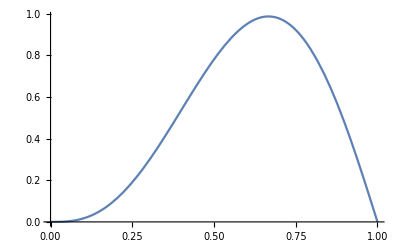

```mathematica
(*Plotting the function for all p between 0 and 1*)
Plot[5 p^3 (4-7 p+3 p^2), {p, 0, 1}]
```

```mathematica
5 p^3 (4-7 p+3 p^2) /. p->0.2
```

0.1088

```mathematica
Solve[301*m + 20*a + 12*t == 1416, {m, a, t}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{t→118-(5 a)/3-(301 m)/12}}

```mathematica
Solve[(100m+10a+1m)+(100m+10a+1t)+(100m+10t+1t)==1416 && 0≤m<10 && 0≤a<10 && 0≤t<10,{m, a, t}, Integers]
```

{{m→4,a→7,t→6}}